```mathematica
model="phi";
loadNotebook["inz_off_model_"<>model<>".nb"];
q̇ // Simplify // MF
```

(R (Sin[θ_0] η_1+Cos[θ_0] Cos[ϕ_1] η_2+(Sin[θ_0] Sin[θ_1]-Cos[θ_0] Cos[θ_1] Sin[ϕ_1]) η_3)
R (-Cos[θ_0] η_1+Cos[ϕ_1] Sin[θ_0] η_2-(Cos[θ_0] Sin[θ_1]+Cos[θ_1] Sin[θ_0] Sin[ϕ_1]) η_3)
(R (-Cos[ϕ_1] η_2+Cos[θ_1] Sin[ϕ_1] η_3+Cos[ϕ_2] η_4-Cos[θ_2] Sin[ϕ_2] η_5))/(2 l)
η_1
η_2
η_3
η_1+Sin[θ_1] η_3-Sin[θ_2] η_5
η_4
η_5)

```mathematica
wyliczSterowanie[w_,wd_,k1_,k2_]:=(
(*Det[D[w,{q[t]}].G2] // Simplify // Print;*)(*phi = Cos[Subscript[ϕ, 1][t]] Cos[Subscript[ϕ, 2][t]], psi =  Cos[Subscript[ϕ, 1][t]] Cos[Subscript[ϕ, 2][t]] Csc[Subscript[θ, 2][t]]*)
uklad=Transpose[G2.Transpose[{{Subscript[η, 1][t],Subscript[η, 2][t],Subscript[η, 3][t],Subscript[η, 4][t],Subscript[η, 5][t]}}]][[1]];
podstawienie = {D[x[t],t]->uklad[[1]],D[y[t],t]->uklad[[2]],D[Subscript[θ, 0][t],t]->uklad[[3]],D[Subscript[ϕ, 1][t],t]->uklad[[4]],D[Subscript[θ, 1][t],t]->uklad[[5]],D[Subscript[ψ, 1][t],t]->uklad[[6]],D[Subscript[ϕ, 2][t],t]->uklad[[7]],D[Subscript[θ, 2][t],t]->uklad[[8]],D[Subscript[ψ, 2][t],t]->uklad[[9]]};
wp=D[w,t]/.podstawienie;
wpp = D[wp,t]/.podstawienie;
Kdd={Coefficient[wpp,D[Subscript[η, 1][t],t]],Coefficient[wpp,D[Subscript[η, 2][t],t]],Coefficient[wpp,D[Subscript[η, 3][t],t]],Coefficient[wpp,D[Subscript[η, 4][t],t]],Coefficient[wpp,D[Subscript[η, 5][t],t]]} // Transpose;
Det[Kdd]// Simplify // Print;
P =wpp-Kdd.{D[Subscript[η, 1][t],t],D[Subscript[η, 2][t],t],D[Subscript[η, 3][t],t],D[Subscript[η, 4][t],t],D[Subscript[η, 5][t],t]};
K1 = k1*IdentityMatrix[5];
K2 = k2*IdentityMatrix[5];
sterowanie=Inverse[Kdd].(-P+D[D[wd,t],t]-K1.(D[w,t]-D[wd,t])-K2.(w-wd)) /. {l-> 0.1, Subscript[r, 1]->0.02, Subscript[r, 2]->0.02};
sterowanie
);

rozwiazRownania[sterowanie_,q0_,tmax_]:=(
pstrona = Transpose[G2.Transpose[{η[t]}]][[1]];
lstrona = D[q[t],t];
lstrona = Join[lstrona,D[η[t],t]];
pstrona = Join[pstrona, sterowanie];
rownanie = Apply[Equal, Transpose[{lstrona, pstrona}],1];
tosolve = (rownanie /.{ l-> 0.1, R-> 0.03}) ~Join~ q0;
roz = NDSolve[tosolve, {x,y, Subscript[θ, 0],Subscript[ϕ, 1], Subscript[θ, 1],Subscript[ψ, 1], Subscript[ϕ, 2], Subscript[θ, 2],Subscript[ψ, 2],Subscript[η, 1],Subscript[η, 2],Subscript[η, 3],Subscript[η, 4],Subscript[η, 5]}, {t,0,tmax}, Method->Automatic, MaxSteps->10000000];
roz
);

wyrysuj[rozwiazanie_, tmax_,anim_,i_]:=Module[{},
loc="C:\\Users\\Admin\\Documents\\GitHub\\hog\\Magisterka\\doc - off\\";

plot1=Plot[{x[t]-xd[t]/.rozwiazanie,y[t]-yd[t]/.rozwiazanie},{t,0,tmax},AxesLabel->{"t","e"},PlotLegends->Placed[{"e_x","e_y"},{0.90,0.75}],PlotRange->{-0.1,0.1}, PlotStyle->{Thick}];
plot1//Print;
Export[loc<>"inz_off_"<>model<>"_lin_dyn_"<>ToString[i]<>"_1.pdf",plot1];

plot2=Plot[{Subscript[θ, 0][t]-θd[t]/.rozwiazanie,Subscript[ψ, 1][t]-wirowanie*t/.rozwiazanie,Subscript[ψ, 1][t]-wirowanie*t/.rozwiazanie},{t,0,tmax},AxesLabel->{"t","e"},PlotLegends->Placed[{"e_θ_0","e_ψ_1","e_ψ_2"},{0.90,0.75}],PlotRange->{-0.1,0.1}, PlotStyle->{Thick}];
plot2//Print;
Export[loc<>"inz_off_"<>model<>"_lin_dyn_"<>ToString[i]<>"_2.pdf",plot2];

If[model=="psi",
zoomStart=12;
range=0.03;
g=Graphics[{EdgeForm[Thick],White,Disk[],Inset[Plot[{Subscript[η, 1][t]/.rozwiazanie,Subscript[η, 5][t]/.rozwiazanie},{t,zoomStart-range,zoomStart+range},Axes->{True,False},ImageSize->140,Ticks->{{zoomStart-range,zoomStart,zoomStart+range},{-1,1}}]]},ImageSize->150];
plot3=Plot[{Subscript[η, 1][t]/.rozwiazanie,Subscript[η, 5][t]/.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","η-ϕ"},PlotLegends->Placed[{"η_1","η_4"},{0.90,0.75}],Axes->{True, True},Epilog->{Inset[g,{40,-100}]}];
plot3//Print;
Export[loc<>"inz_off_"<>model<>"_lin_dyn_"<>ToString[i]<>"_3.pdf",plot3];,

zoomStart=12;
range=0.03;
g=Graphics[{EdgeForm[Thick],White,Disk[],Inset[Plot[{Subscript[η, 1][t] /.rozwiazanie},{t,zoomStart-range,zoomStart+range},Axes->{True,False},ImageSize->140,Ticks->{{zoomStart-range,zoomStart,zoomStart+range},{-1,1}}]]},ImageSize->150];
plot3=Plot[{Subscript[η, 1][t] /.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","η-ϕ"},PlotLegends->Placed[{"η_1","η_4"},{0.90,0.75}],Axes->{True, True},Epilog->{Inset[g,{40,-100}]}];
plot3//Print;
Export[loc<>"inz_off_"<>model<>"_lin_dyn_"<>ToString[i]<>"_3.pdf",plot3];
];

If[model=="psi",
plot4=Plot[{M[[2]] /.rozwiazanie,M[[5]] /.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","η-θ"},PlotLegends->Placed[{"η_2","η_5"},{0.90,0.75}],Axes->{True, True}];
plot4//Print;
Export[loc<>"inz_off_"<>model<>"_lin_dyn_"<>ToString[i]<>"_4.pdf",plot4];,

plot4=Plot[{Subscript[η, 2][t] /.rozwiazanie,Subscript[η, 4][t] /.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","η-θ"},PlotLegends->Placed[{"η_2","η_4"},{0.90,0.75}],Axes->{True, True}];
plot4//Print;
Export[loc<>"inz_off_"<>model<>"_lin_dyn_"<>ToString[i]<>"_4.pdf",plot4];
];

plot5=Plot[{Subscript[ϕ, 1][t] /.rozwiazanie,Subscript[ϕ, 2][t] /.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","ϕ"},PlotLegends->Placed[{"ϕ_1","ϕ_2"},{0.90,0.75}],Axes->{True, True}];
plot5//Print;
Export[loc<>"inz_off_"<>model<>"_lin_dyn_"<>ToString[i]<>"_5.pdf",plot5];

plot6=Plot[{Subscript[θ, 1][t] /.rozwiazanie,Subscript[θ, 2][t] /.rozwiazanie}, {t,0,tmax}, PlotRange->All, AxesLabel->{"t","θ"},PlotLegends->Placed[{"θ_1","θ_2"},{0.90,0.75}],Axes->{True, True}];
plot6//Print;
Export[loc<>"inz_off_"<>model<>"_lin_dyn_"<>ToString[i]<>"_6.pdf",plot6];

plot7=Plot[{Subscript[ψ, 1]'[t] /.rozwiazanie,Subscript[ψ, 2]'[t] /.rozwiazanie}, {t,0,tmax}, PlotRange->{495,505}, AxesLabel->{"t","ψ̇"},PlotLegends->Placed[{"(ψ̇)_1","(ψ̇)_2"},{0.90,0.75}],Axes->{True, True}];
plot7//Print;
Export[loc<>"inz_off_"<>model<>"_lin_dyn_"<>ToString[i]<>"_7.pdf",plot7];

krzywa1[t_] = {x[t] ,y[t]} /. rozwiazanie;

p1[t_] = ((Agms[x[t], y[t], Subscript[θ, 0][t]]/.rozwiazanie).Transpose[{{0,0,0,1}}]) /. {l-> 0.1, R-> 0.03};
x1[t_] = (p1[t])[[1,1,1]];
y1[t_] = (p1[t])[[1,2,1]];
krzywas[t_] = {x1[t], y1[t]} /. rozwiazanie;

p2[t_] = ((Agm2[x[t], y[t], Subscript[θ, 0][t]]/.rozwiazanie).Transpose[{{0,0,0,1}}]) /. {l-> 0.1, R-> 0.03};
x2[t_] = (p2[t])[[1,1, 1]];
y2[t_] = (p2[t])[[1,2, 1]];
krzywa2[t_] = {x2[t], y2[t]}/. rozwiazanie;

ẋ[t_] = (x1'[t] /.rozwiazanie)[[1]];
ẏ[t_] = (y1'[t] /. rozwiazanie)[[1]];
v[t_] = Re[Sqrt[(ẋ[t])^2+(ẏ[t])^2]];

krzywad[t_]={xd[t],yd[t]};

a1 = Animate[
Show[
{Plot[v[t], {t, 0, tmax}, PlotRange->All,AxesLabel->{"t","v"}]},
{
Graphics[{PointSize[Large],Red,Point[Dynamic[{t,v[t]}]]}]
}
],{t,0,tmax}];

curvs = ParametricPlot[{krzywas[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->{Red}, Axes->{True, True}, AxesOrigin->{0,0}];
curv1 = ParametricPlot[{krzywa1[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Blue}, Axes->{True, True},AxesOrigin->{0,0}];
curv2 = ParametricPlot[{krzywa2[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Yellow}, Axes->{True, True}, AxesOrigin->{0,0}];
curvd = ParametricPlot[{krzywad[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Black}, Axes->{True, True}, AxesOrigin->{0,0}];

plot8=ParametricPlot[{krzywa1[t],krzywad[t]},{t, 0, tmax},PlotRange->All,PlotStyle->{Red,Black}, Axes->{True, True}, AxesOrigin->{0,0}];
plot8//Print;
Export[loc<>"inz_off_"<>model<>"_lin_dyn_"<>ToString[i]<>"_8.pdf",plot8];


p11[t_]=Evaluate[{x[t],y[t]}/.rozwiazanie];
p22[t_]=Evaluate[{x2[t],y2[t]}/.rozwiazanie];
x11[t_]=(x[t]/.rozwiazanie)[[1]];
y11[t_]=(y[t]/.rozwiazanie)[[1]];
x22[t_]=(x2[t]/.rozwiazanie)[[1]];
y22[t_]=(y2[t]/.rozwiazanie)[[1]];
a2=Animate[
Show[
{curvs,curv1,curv2,curvd},
{
Graphics[{PointSize[0.03],Red,Point[Dynamic[p11[t]]]}],
Graphics[{PointSize[0.03], Red,Point[Dynamic[p22[t]]]}],
Graphics[{PointSize[0.02], Black,Point[Dynamic[{xd[t],yd[t]}]]}],
Graphics[
{Thickness[0.002],Green,
Line[
{
Dynamic[{x11[t],y11[t]}],
Dynamic[{x2[t],y2[t]}]
}
]
}]
}
],{t,0,tmax}];
If[anim,Print[a1],0];
If[anim,Print[a2],0];
0
];
```

-(R^3 Cos[ϕ_1[t]] Cos[ϕ_2[t]])/(2 l)

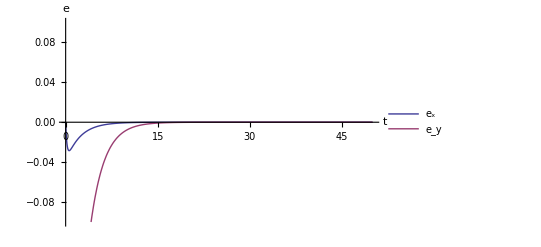

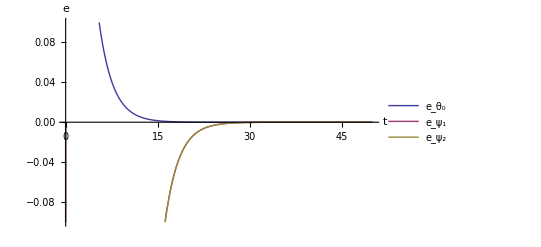

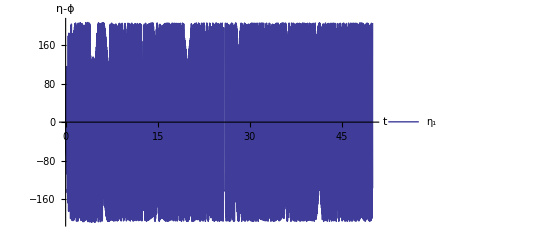

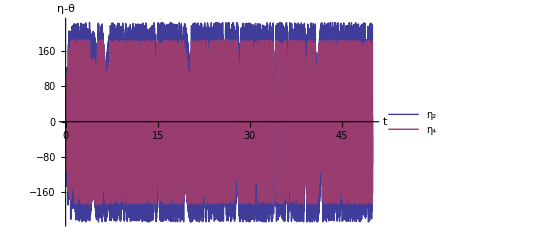

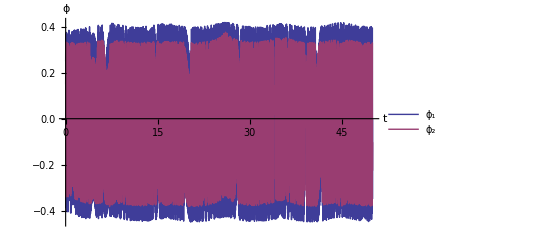

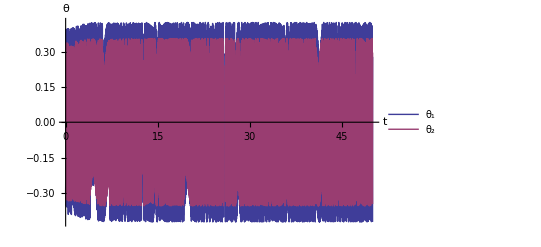

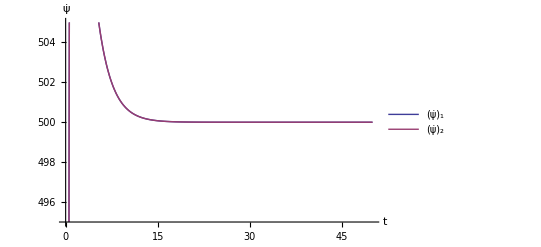

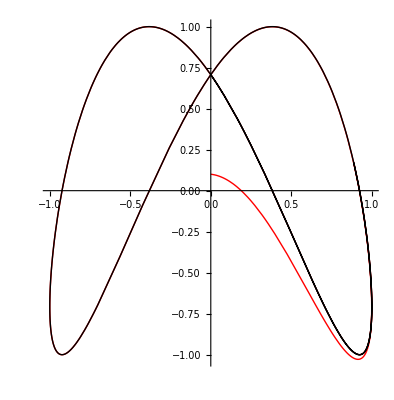

```mathematica
w={x[t],y[t],Subscript[θ, 0][t],Subscript[ψ, 1][t],Subscript[ψ, 2][t]};
wirowanie = 500;
tmax=50;
q0={x[0]== 0, y[0]==0.1, Subscript[θ, 0][0]==0, Subscript[ϕ, 1][0]==0.25, Subscript[θ, 1][0]== -0.3, Subscript[ψ, 1][0]==0,Subscript[ϕ, 2][0]== 0.15, Subscript[θ, 2][0]==-0.3, Subscript[ψ, 2][0]==0, Subscript[η, 1][0]==0, Subscript[η, 2][0]==0, Subscript[η, 3][0]==0, Subscript[η, 4][0]==0, Subscript[η, 5][0]==0};
{xd[t_],yd[t_]}=osemka[t,3];
θd[t_] = If[ArcTan[xd'[t],yd'[t]]>-Pi/2,ArcTan[xd'[t],yd'[t]],ArcTan[xd'[t],yd'[t]]+2Pi];
wd = {xd[t],yd[t], θd[t], wirowanie*t, wirowanie*t};
sterowanie = wyliczSterowanie[w,wd,5,2]//Simplify;
rozwiazanie = rozwiazRownania[sterowanie, q0, tmax];
wyrysuj[rozwiazanie,tmax,True,1];
```

```mathematica
data = Table[(Subscript[η, 1][t] /.rozwiazanie)[[1]],{t,0,tmax,1/1000}];
Periodogram[data,SampleRate->1000,PlotRange->All]//Print
```

0

-(R^3 Cos[ϕ_1[t]] Cos[ϕ_2[t]])/(2 l)

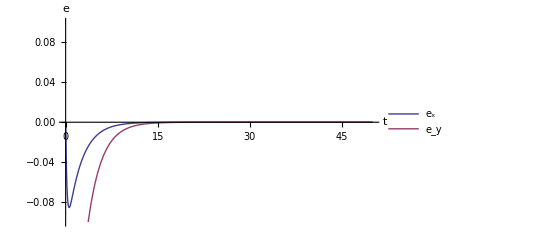

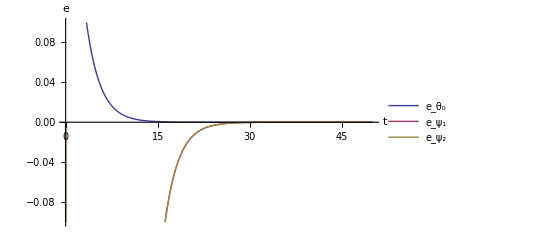

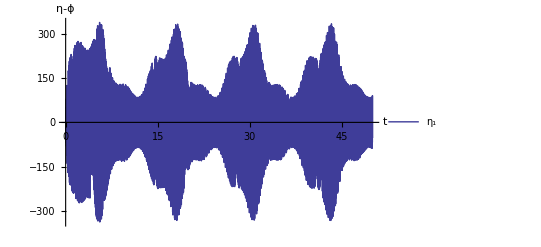

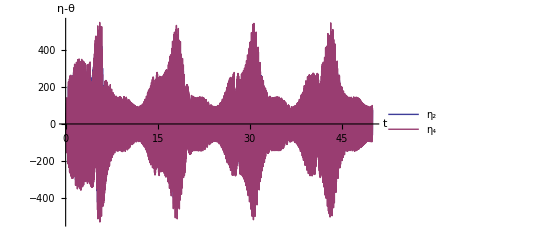

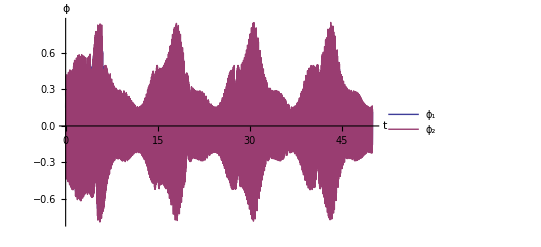

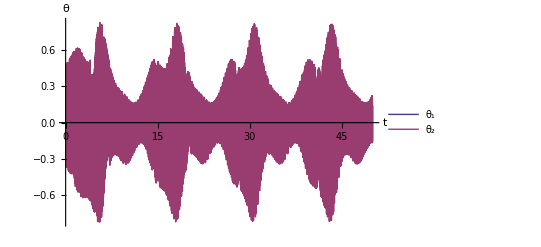

-Graphics-

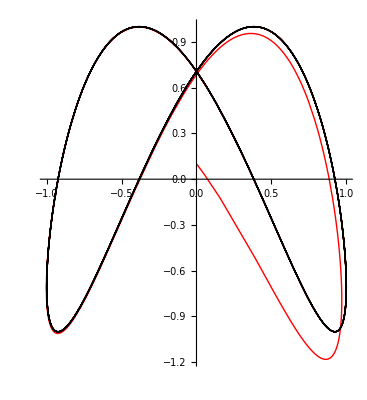

1

-(R^3 Cos[ϕ_1[t]] Cos[ϕ_2[t]])/(2 l)

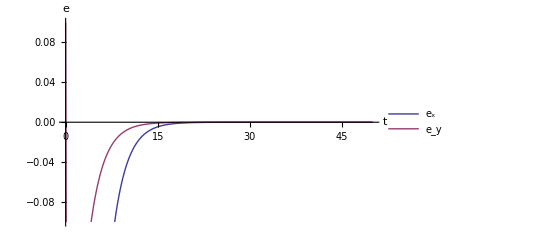

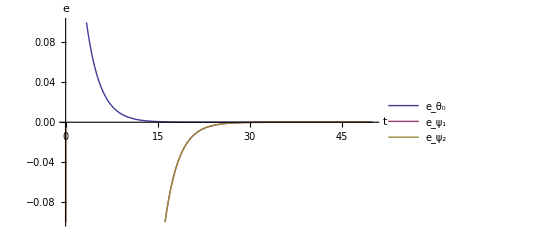

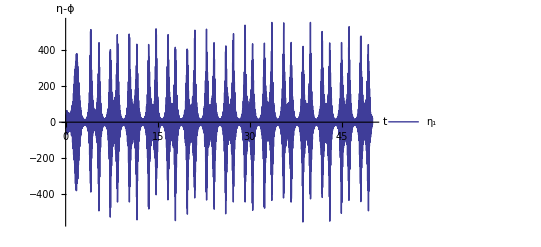

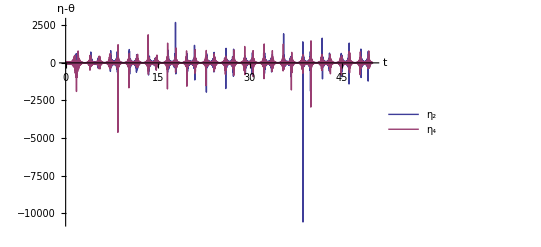

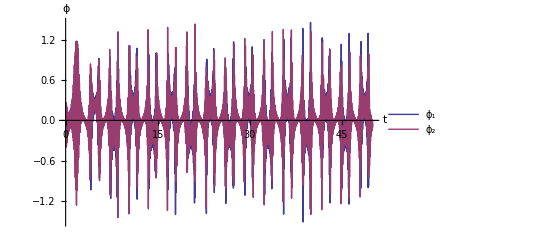

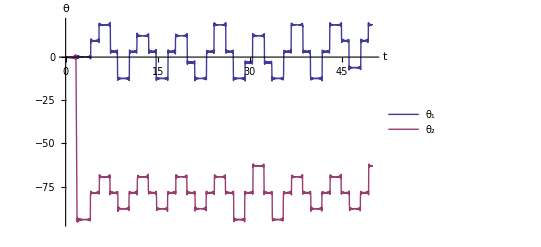

-Graphics-

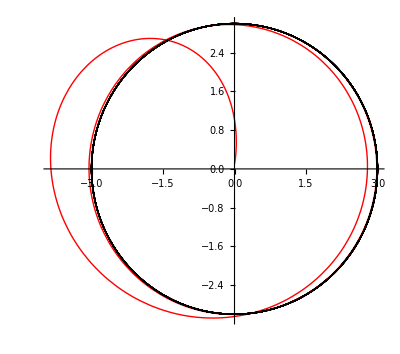

2

-(R^3 Cos[ϕ_1[t]] Cos[ϕ_2[t]])/(2 l)

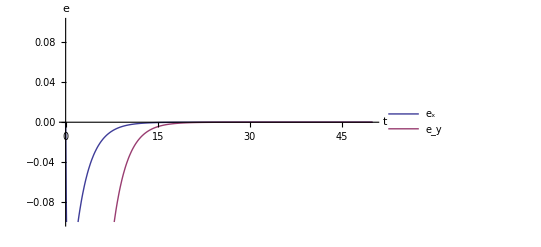

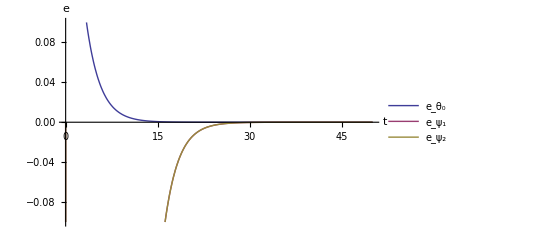

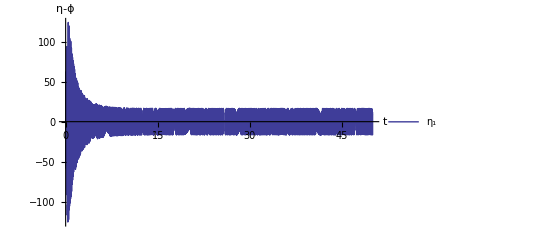

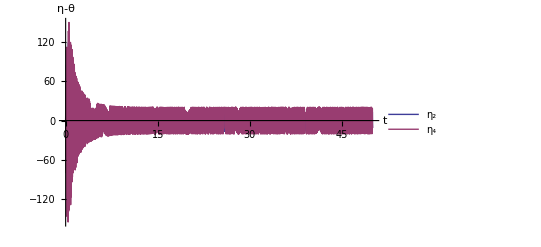

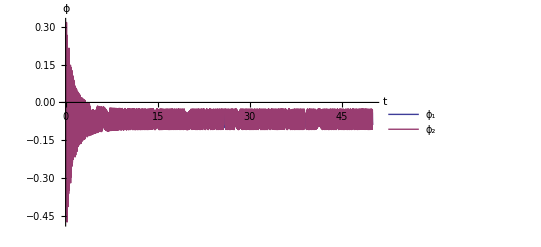

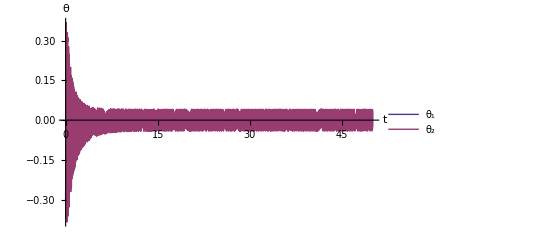

-Graphics-

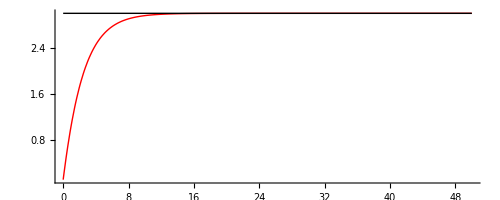

3

-(R^3 Cos[ϕ_1[t]] Cos[ϕ_2[t]])/(2 l)

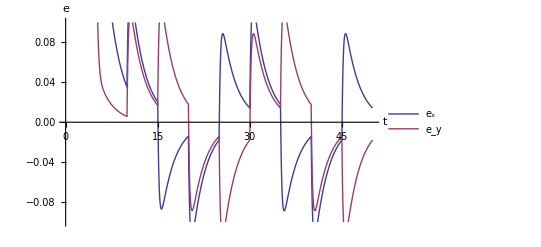

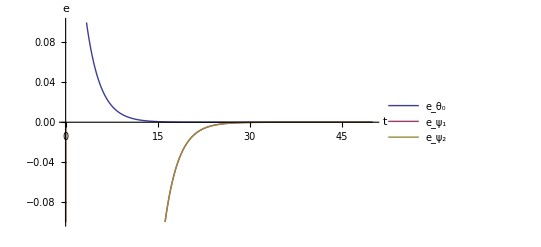

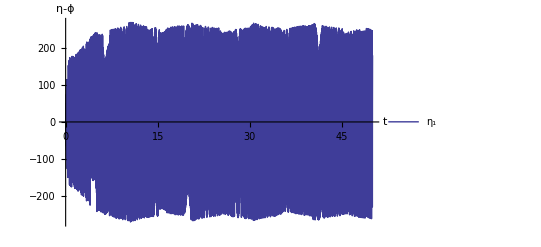

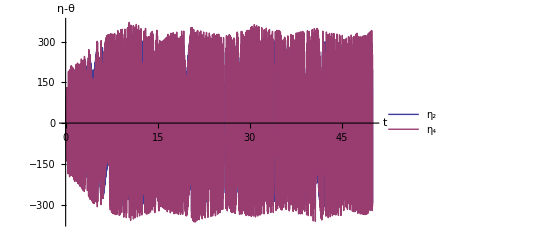

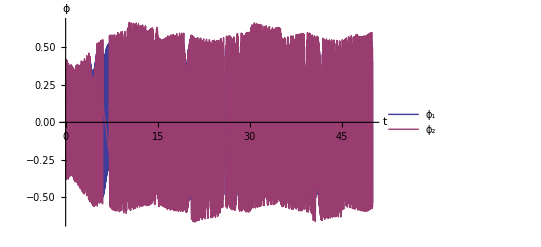

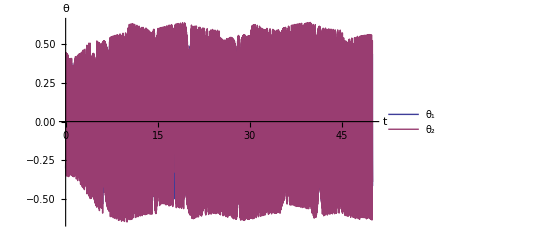

-Graphics-

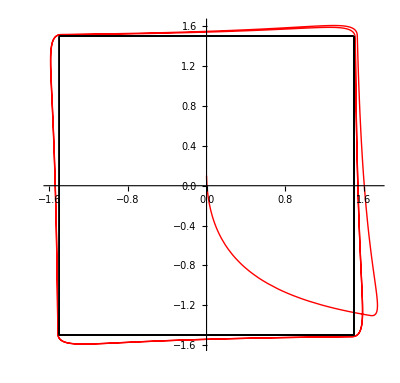

```mathematica
w={x[t],y[t],Subscript[θ, 0][t],Subscript[ψ, 1][t],Subscript[ψ, 2][t]};
wirowanie = 500;
tmax=50;
q0={x[0]== 0, y[0]==0.1, Subscript[θ, 0][0]==0.4, Subscript[ϕ, 1][0]==0.15, Subscript[θ, 1][0]== -0.3, Subscript[ψ, 1][0]==0,Subscript[ϕ, 2][0]== 0.25, Subscript[θ, 2][0]==-0.3, Subscript[ψ, 2][0]==0, Subscript[η, 1][0]==0, Subscript[η, 2][0]==0, Subscript[η, 3][0]==0, Subscript[η, 4][0]==0, Subscript[η, 5][0]==0};

For[i=0,i<4,i++,
Print[i];
Which[i==0,{xd[t_],yd[t_]}=osemka[t,1],i==1,{xd[t_],yd[t_]}=kolo[t,3,1],i==2,{xd[t_],yd[t_]}=liniaX[t,3,1],True,{xd[t_],yd[t_]}=kwadrat[t,3,5]];
θd[t_] = 0;(*ArcTan[xd[t],yd[t]]*);
wd = {xd[t],yd[t], θd[t], wirowanie*t, wirowanie*t};
sterowanie = wyliczSterowanie[w,wd,5,2];
rozwiazanie = rozwiazRownania[sterowanie,q0,tmax];
wyrysuj[rozwiazanie, tmax,False];
];
```